```mathematica
Integrate[1+Cos[x]^2,{x,0,2*π}]
```

3 π

```mathematica
data=Table[(3x+0.5*Sin[2x])/(6π),{x,0,6.2832,0.0001}]
```

{0.,0.0000212207,0.0000424413,0.000063662,0.0000848826,62823,0.999918,0.999939,0.999961,0.999982,1.}
 |  |  |  |

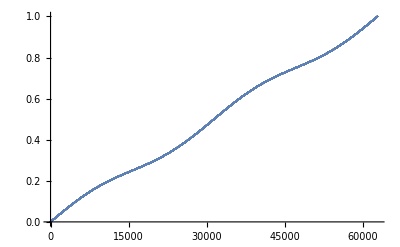

```mathematica
ListPlot[data]
```

```mathematica
no[λ_]:=((8060.51+2480990/(132.274-λ^-2)+17455.7/(39.32957-λ^-2))/10^8)+1
```

```mathematica
fk[λ_]:=1.034+(3.17*10^-4)/λ^2(*For a 100% Subscript[N, 2] Atmosphere*)
```

```mathematica
Ns=2.54743*10^19;(*1/cm^3*)
```

```mathematica
σ[λ_]:=(24*π^3)/((λ/10^7)^4*Ns^2)*((no[(λ/1000)]^2-1)^2)/((no[(λ/1000)]^2+2)^2)*fk[(λ/1000)](*cm^2*)
```

```mathematica
P=101325.0(*in Pa*);R=8.3144598(* Pa*);T=288.15(*in K*);Na=6.022140857*10^23(*moles/mol*);
```

```mathematica
τ[λ_]:=σ[λ]*10^-6*(P*Na)/(R*T)
```

```mathematica
σ[450]
```

1.01271×10^-26

```mathematica
τ[450]
```

2.57929×10^-7

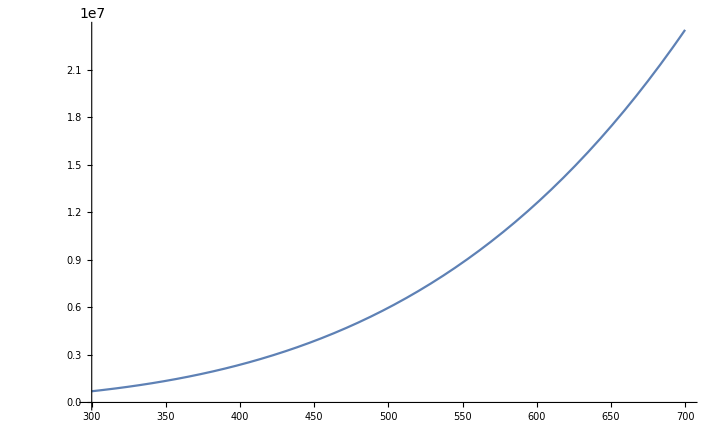

```mathematica
Plot[1/τ[λ],{λ,300,700}](*λ in nm*)
```